# Elastica solution

Initialization

```mathematica
Quiet@Unprotect["Notation`*"];
Quiet[ClearAll[#] ]& /@ {"Global`*", "Love`ComplexSymbols`*","ComplexSymbols`*","Notation`*"};
Quiet[Remove[#] ]& /@ {"Global`*", "Love`ComplexSymbols`*","ComplexSymbols`*","Notation`*"};
<<MaTeX`
(*<<Notation`*)
```

```mathematica
Begin["Love`"]
Needs["ComplexSymbols`", URLDownload["https://raw.githubusercontent.com/haneeshk/ForBetterMMAExperience/master/ComplexSymbols.wl"]]
If[ValueQ[syms], UnassignLabels[syms];ClearAll[syms]];
If[ValueQ[sympaltte],NotebookClose[sympaltte]; ClearAll[sympaltte]]
syms=AssignLabels[{"θ","θ'","θ''","k_n"}];
sympaltte=SymbolPalette["syms",syms,1];
x::usage="x cordinate";
y::usage="y cordinate"
End[]
AppendTo[$ContextPath, "Love`"]
```

Love`

Complex Symbols Package Loaded

y cordinate

Love`

{ComplexSymbols`,MaTeX`,WolframAlphaClient`,CloudPublishMenu`,SystemTools`,ExternalEvaluateLoader`,PacletManager`,System`,Global`,Love`}

```mathematica
MaTeX[HoldForm[θ''+p Sin[θ]=0],FontSize->18];
MaTeX[HoldForm[x'[s]=Cos[θ[s]]],FontSize->18];
MaTeX[HoldForm[y'[s]=Sin[θ[s]]],FontSize->18];
```

θ[s] = 2 sin^-1[√k_n sn[s √p+K[k_n];k_n]]
K[k_n]=√p/2;

```mathematica
ClearAll["θ","θ''"]
"θ"[s_,p_,"k_n":_]=2 ArcSin[Sqrt["k_n"] JacobiSN[s Sqrt[p]+EllipticK["k_n"],"k_n"]] ;      (*From Love's book*)
"θ'"[s_,p_,"k_n":_]=(D["θ"[s,p,"k_n"],{s,1}]//FullSimplify);
"θ''"[s_,p_,"k_n":_]=(D["θ"[s,p,"k_n"],{s,2}]//FullSimplify);
Labeled["θ"[s,p,"k_n"],"StyleBox["θ",FontFamily->"Times New Roman",FontSize->18,FontWeight->"Regular"][s;p, SubscriptBox[StyleBox["k",FontFamily->"Times New Roman",FontSize->18,FontWeight->"Regular",FontSlant->"Italic"], StyleBox["n",FontFamily->"Times New Roman",FontSize->14,FontWeight->"Regular"]]] =",Left]
Labeled["θ''"[s,p,"k_n"],"StyleBox["θ",FontFamily->"Times New Roman",FontSize->18,FontWeight->"Regular"]StyleBox["''",FontFamily->"Times New Roman",FontSize->18,FontWeight->"Regular"][s;p,SubscriptBox[StyleBox["k",FontFamily->"Times New Roman",FontSize->18,FontWeight->"Regular",FontSlant->"Italic"], StyleBox["n",FontFamily->"Times New Roman",FontSize->14,FontWeight->"Regular"]]] =",Left]


x[s_,p_,"k_n":_]=-s+2/Sqrt[p](EllipticE[JacobiAmplitude[s Sqrt[p]+EllipticK["k_n"],"k_n"],"k_n"]-EllipticE[JacobiAmplitude[EllipticK["k_n"],"k_n"],"k_n"]);
y[s_,p_,"k_n":_]=-2 Sqrt["k_n"]/Sqrt[p] JacobiCN[s Sqrt[p]+EllipticK["k_n"],"k_n"];
```

2 ArcSin[√k_n JacobiCD[√p s,k_n]]StyleBox["θ",FontFamily->"Times New Roman",FontSize->18,FontWeight->"Regular"][s;p, SubscriptBox[StyleBox["k",FontFamily->"Times New Roman",FontSize->18,FontWeight->"Regular",FontSlant->"Italic"], StyleBox["n",FontFamily->"Times New Roman",FontSize->14,FontWeight->"Regular"]]] =

-(2 (-1+k_n)^2 √k_n p JacobiCN[√p s,k_n])/((1-k_n JacobiCD[√p s,k_n]^2)^(3/2) JacobiDN[√p s,k_n]^5)StyleBox["θ",FontFamily->"Times New Roman",FontSize->18,FontWeight->"Regular"]StyleBox["''",FontFamily->"Times New Roman",FontSize->18,FontWeight->"Regular"][s;p,SubscriptBox[StyleBox["k",FontFamily->"Times New Roman",FontSize->18,FontWeight->"Regular",FontSlant->"Italic"], StyleBox["n",FontFamily->"Times New Roman",FontSize->14,FontWeight->"Regular"]]] =

```mathematica
ClearAll["k_n"]
"k_n"[p_]:=Module[{solk},
x/.FindRoot[EllipticK[x] - Sqrt[p]/2,{x,0.1}]
]
```

```mathematica
"k_n"[ π^2+0.4]
```

0.0767507

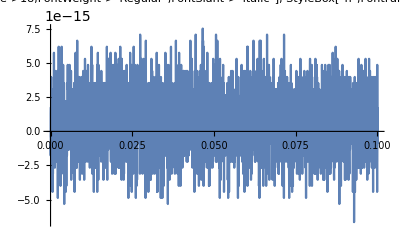

```mathematica
Module[{p= π^2+0.2},
Plot["θ''"[s,p,"k_n"[p]]+p Sin["θ"[s,p,"k_n"[p]]],{s,0,.1},PlotLabel->Grid[{{"SubscriptBox[StyleBox["k",FontFamily->"Times New Roman",FontSize->18,FontWeight->"Regular",FontSlant->"Italic"], StyleBox["n",FontFamily->"Times New Roman",FontSize->14,FontWeight->"Regular"]] =","k_n"[p]}}]]
]
```

```mathematica
ClearAll[ColumnShapeFromLoveθ]
ColumnShapeFromLoveθ[p_]:=Module[{soly,solx,x,y,δ},
solx =NDSolve[{x'[s]==Cos["θ"[s,p,"k_n"[p]]],x[0]==0},x[s],{s,0,1}];
soly= NDSolve[{y'[s]==Sin["θ"[s,p,"k_n"[p]]],y[0]==0},y[s],{s,0,1}];
δ = y[s]/.soly[[1]]/.s->1/2;
ParametricPlot[{x[s]/.solx[[1]],y[s]/.soly[[1]]},{s,0,1},PlotStyle->{Black},ImageSize->Large,PlotLabel->Grid[{{"δ =",δ}}],PlotRange->{{-0.5,1.5},{0,0.5}}]
]
```

```mathematica
Manipulate[ColumnShapeFromLoveθ[p],{p,π^2+0.1,5 π^2}]
```

```mathematica
ClearAll[ColumnShapeFromLovexy]
ColumnShapeFromLovexy[p_]:=Module[{},
ParametricPlot[{Chop[x[s,p,"k_n"[p]],10^-6],y[s,p,"k_n"[p]]},{s,0,1},PlotRange->All,PlotStyle->{Green,Dashed},ImageSize->Large]
]
```

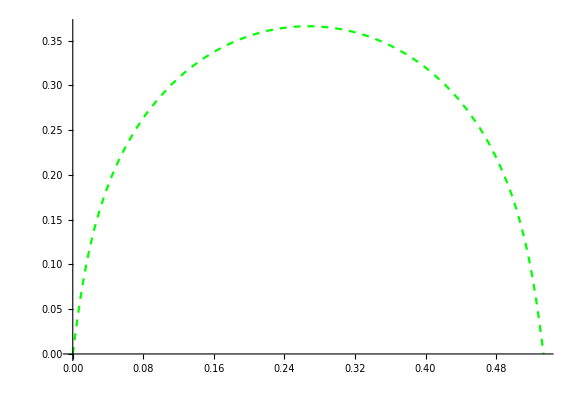

```mathematica
ColumnShapeFromLovexy[13]
```

```mathematica
ClearAll[ColumnShapeFromMMA]
ColumnShapeFromMMA[p_]:=Module[{solMM,MMθ2,solx,soly,dflection,x,y,θ},
solMM=NDSolve[{θ''[s]+p Sin[θ[s]]==0,θ'[0]==0,θ'[1]==0},θ[s],{s,0,1}];
solx =NDSolve[{x'[s]==Cos[θ[s]/.solMM[[1]]],x[0]==0},x[s],{s,0,1}];
soly= NDSolve[{y'[s]==Sin[θ[s]/.solMM[[1]]],y[0]==0},y[s],{s,0,1}];
dflection = y[s]/.soly[[1]]/.s->1/2;
ParametricPlot[{x[s]/.solx[[1]],Abs[y[s]/.soly[[1]]]},{s,0,1},PlotRange->All,PlotStyle->{Opacity[0.5],Thickness[0.02],ColorData[2][1]},ImageSize->Large]
]
```

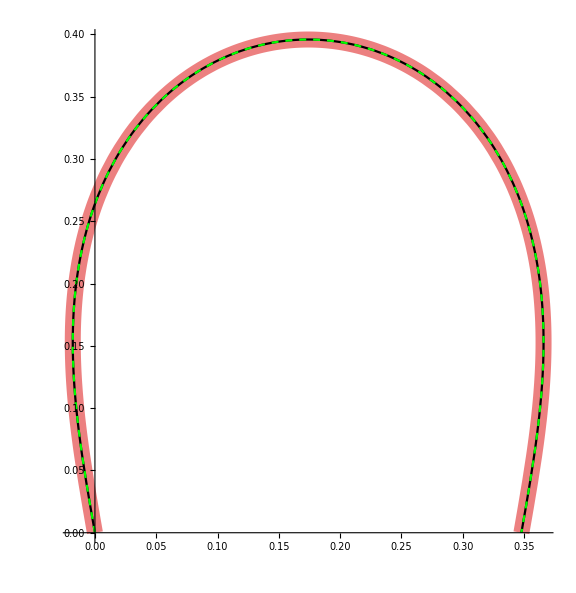

```mathematica
Show[ColumnShapeFromMMA[15],ColumnShapeFromLoveθ[15],ColumnShapeFromLovexy[15]]
```

Log:
1. All equations from Love’s book are correct. They have been validated using Direct numerical calculations

```mathematica
SymbolPalette["syms",syms,1]
```

j6734_shm375FrontEndObject[LinkObject["j6734_shm", 3, 1]]375syms

```mathematica
Limit["θ'"[s,p,k],s->0]
```

0

```mathematica
?ComplexSymbols`*
```

```mathematica
ClearAll[ColumnShapeRotate]
ColumnShapeRotate[p1_,p2_]:=Module[{solMM,MMθ2,solx,soly,solk,dflection,x,y,θ,θ0,θ1,p,span},
p =Sqrt[p1^2+p2^2];
θ0=ArcTan[p1,p2];
solk = FindRoot["θ"[1/2,p,k]-θ0,{k,0.7}];
θ1[s_]=("θ"[s,p,Re[k]]/.solk[[1]])-θ0;
solx =NDSolve[{x'[s]==Cos[θ1[s]],x[0]==0},x[s],{s,0,1/2}];
soly= NDSolve[{y'[s]==Sin[θ1[s]],y[0]==0},y[s],{s,0,1/2}];
dflection = y[s]/.soly[[1]]/.s->1/2;
span =2(x[s]/.solx[[1]]/.s->1/2);
Show[
ParametricPlot[{x[s]/.solx[[1]],Abs[y[s]/.soly[[1]]]},{s,0,1/2},PlotRange->All,PlotStyle->{Opacity[1],Thickness[0.002],ColorData[2][1]},ImageSize->Large],
ParametricPlot[{span-x[s]/.solx[[1]],Abs[y[s]/.soly[[1]]]},{s,0,1/2},PlotRange->All,PlotStyle->{Opacity[1],Thickness[0.002],ColorData[2][1]},ImageSize->Large]]
]
```

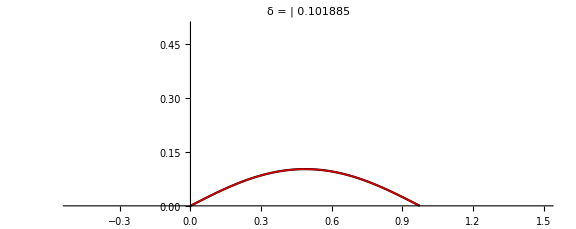

```mathematica
Show[ColumnShapeFromLoveθ[10],ColumnShapeRotate[10,0]]
```

```mathematica
Manipulate[ColumnShapeRotate[p1,p2],{p1,10,20},{p2,0,10}]
```